## Model Setup

```mathematica
wm = ResourceFunction["WolframModel"];
plot = ResourceFunction["WolframModelPlot"];
randomRule = ResourceFunction["RandomWolframModel"];
```

```mathematica
steps=10;
maxValue = 3;
maxVertices=3;
```

```mathematica
randomSignature[maxRelations_, maxElements_, maxPieces_] := 
	Rule @@ Table[
		Table[
			{RandomInteger[{1, maxRelations}], RandomInteger[{1, maxElements}]},
			RandomInteger[{1, maxPieces}]
		], 
		2
	]
```

```mathematica
signature = randomSignature[3, 3, 2]
```

{{3,1}}→{{2,1},{3,3}}

```mathematica
signature={{2,2}}->{{4,2}}
```

```mathematica
{{2,2}}->{{3,2}}
```

{{2,2}}→{{3,2}}

```mathematica
init = Array[Function[1],signature[[1]][[1]]]
```

{{1,1},{1,1}}

```mathematica
rule=randomRule[signature]
```

{{1,2},{3,2}}→{{4,1},{4,2},{5,4},{3,1}}

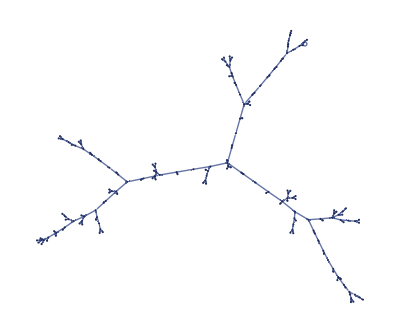

```mathematica
wm[rule, init, steps, "FinalStatePlot"]
```

```mathematica
gOrig = wm[rule, init,steps,"FinalState"]
```

{{1,2},{1,3},{2,5},{2,6},{5,8},{5,9},{8,11},{8,12},{11,14},{11,15},{14,17},{14,18},{17,20},{17,21},{20,23},{20,24},{23,26},{23,27},{26,29},{26,30},{29,31},{1,31}}

## Mutations

### Simplest case: retain signature, replace only elements with same range

```mathematica
rule ={rule}
```

{{{1,2},{3,2}}→{{4,1},{4,2},{5,4},{3,1}}}

```mathematica
selectElement[rule_]:=
Module[{replacement, side, edge, vertex, x},
replacement=RandomInteger[{1, Length[rule]}];
x = rule[[replacement]];
side = RandomInteger[{1, 2}];
x = x[[side]];
edge = RandomInteger[{1, Length[x]}];
x = x[[edge]];
vertex = RandomInteger[{1, Length[x]}];
{replacement, side, edge, vertex}
]
```

```mathematica
maxElement[rule_]:=Max[Flatten[List@@@rule]]
```

```mathematica
replaceRandomElement[rule_]:=
ReplacePart[rule, selectElement[rule]->RandomInteger[{1,maxElement[rule]}]]
```

```mathematica
rule
```

{{{1,2},{3,2}}→{{4,1},{4,2},{5,4},{3,1}}}

```mathematica
newRule=replaceRandomElement[rule]
```

{{{1,2},{3,2}}→{{4,1},{4,2},{5,3},{3,1}}}

```mathematica
evolution = wm[newRule, init, steps]
```

WolframModelEvolutionObject[…]

```mathematica
g = Graph@evolution["FinalState"]
```

-Graphics-

```mathematica
largestConnectedSubgraph[g_]:=
Subgraph[g, MaximalBy[ConnectedComponents[g], Length]]
```

### Find rules which give connected graphs of increasing dimension

```mathematica
ruleDimension[rule_]:=graphDimension[Graph[wm[rule, {{1,1},{1,1}}, 7, "FinalState"]]]
```

```mathematica
graphDimension[graph_] := If[ConnectedGraphQ[g],
 	ResourceFunction["WolframHausdorffDimension"][graph,All, "AllDimensions","VertexMethod" -> Max],
0]
```

```mathematica
nextGen[rule_,n_,fitnessFunction_]:=
Module[{baseFitness = fitnessFunction[rule], newRules={}, newRule},
While[Length[newRules]<n,
newRule=replaceRandomElement[rule];
If[!MemberQ[newRules, newRule] && fitnessFunction[newRule]>baseFitness,
AppendTo[newRules, newRule]
]
];
newRules
]
```

```mathematica
newRules = nextGen[rule,5,ruleDimension]
```

{{{{1,2},{4,2}}→{{4,1},{4,2},{5,4},{3,1}}},{{{1,2},{3,5}}→{{4,1},{4,2},{5,4},{3,1}}},{{{1,2},{3,2}}→{{4,1},{1,2},{5,4},{3,1}}},{{{4,2},{3,2}}→{{4,1},{4,2},{5,4},{3,1}}},{{{1,2},{3,4}}→{{4,1},{4,2},{5,4},{3,1}}}}

```mathematica
graphRule[rule_]:=wm[rule,{{1,1},{1,1}},7,"FinalStatePlot"]
```

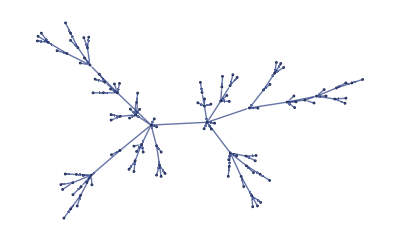
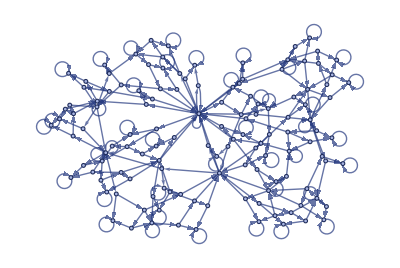
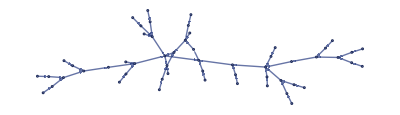
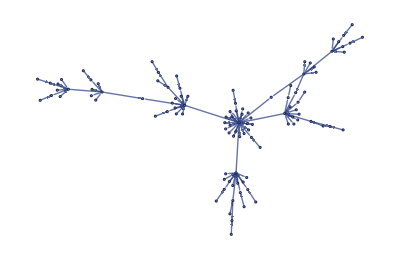
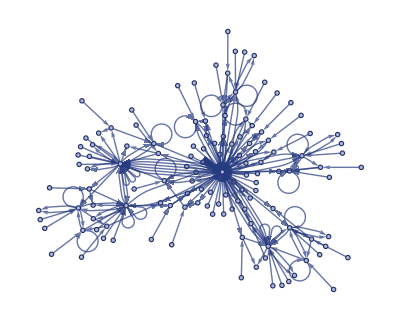

```mathematica
graphRule/@newRules
```